```mathematica
(* Define and plot a function *)
f[x_,θ_]:=1/(θ x^3 + 1)
```

```mathematica
Information[f]
```

```mathematica
Manipulate[Plot[f[x,θ],{x,0,1}],{θ,1,10}]
```

```mathematica
g[x_]:=Piecewise[{{x^2, x<0}, {x, x≥0}}] (* Type ESC + pw + ESC, then CTRL + ENTER *)
```

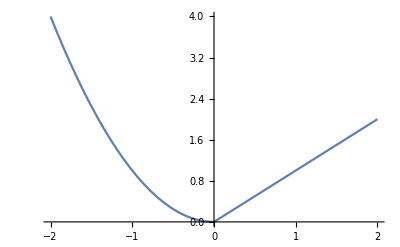

```mathematica
Plot[g[x],{x,-2,2}]
```

```mathematica
(* Take derivatives *)
```

```mathematica
D[f[x,θ],x]
```

-(3 x^2 θ)/((1+x^3 θ)^2)

```mathematica
D[f[x,θ],{x,2}]//Simplify
```

(6 x θ (-1+2 x^3 θ))/((1+x^3 θ)^3)

```mathematica
(* Find integrals *)
```

```mathematica
Integrate[f[x,θ],x]
```

(2 √3 ArcTan[(-1+2 x θ^(1/3))/(√3)]+2 Log[1+x θ^(1/3)]-Log[1-x θ^(1/3)+x^2 θ^(2/3)])/(6 θ^(1/3))

```mathematica
Integrate[f[x,θ]/.θ-> 1,{x,0,1}]
```

1/18 (2 √3 π+Log[64])

```mathematica
LaplaceTransform[f[x,θ],x,s]
```

MeijerG[{{2/3},{}},{{0,1/3,2/3,2/3},{}},s^3/(27 θ)]/(2 √3 π θ^(1/3))

```mathematica
(* Find roots/solve systems of equations *)
(* Let S = sum of n Bernoulli random variables with probability p *)
```

```mathematica
L[p_,n_,S_]:=Binomial[n,S]*p^S*(1-p)^(n-S)
```

```mathematica
Solve[D[L[p,n,S],p]==0,p]
```

{{p→S/n}}

```mathematica
Solve[F[x^2]==a,x]
```

{{x→-√(F^(-1)[a])},{x→√(F^(-1)[a])}}

```mathematica
(* Find probabilities *)
```

```mathematica
Probability[X^2>1\[Conditioned]X>1/2, X\[Distributed]LaplaceDistribution[a,b]]
```

Piecewise[{{ⅇ^(-1/2/b), 2 a≤1}, {(ⅇ^(1/b)-2 ⅇ^(a/b))/(ⅇ^(1/2/b)-2 ⅇ^(a/b)), a≥1}, {ⅇ^((-1+2 a)/b)/(-ⅇ^(1/2/b)+2 ⅇ^(a/b)), True}}]

```mathematica
Probability[X<c,X\[Distributed]UniformDistribution[{a,1}],Assumptions->-1<c<1 && a<c]
```

(-a+c)/(1-a)

```mathematica
(* Empirical distributions *)
```

```mathematica
data=RandomVariate[BinormalDistribution[0],100];
```

```mathematica
dataDist=EmpiricalDistribution[data];
```

```mathematica
Probability[X+Y^2>1,{X,Y}\[Distributed]dataDist]
```

0.49

```mathematica
(* Find density functions *)
```

```mathematica
PDF[SmoothKernelDistribution[data],{0.5,0.5}]
```

0.171854

```mathematica
PDF[BinormalDistribution[1/3],{x,y}]
```

(3 ⅇ^(-9/16 (x^2-(2 x y)/3+y^2)))/(4 √2 π)

```mathematica
Plot3D[%,{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
(* Expectations *)
```

```mathematica
Expectation[(X-1)^2,X\[Distributed]NormalDistribution[μ,σ]]
```

1-2 μ+μ^2+σ^2

```mathematica
(* Distributions of transformed RVs *)
```

```mathematica
dist=TransformedDistribution[X^2,X\[Distributed]BetaDistribution[a,b]];
```

```mathematica
PDF[dist,X]
```

Piecewise[{{((1-√X)^(-1+b) X^(-1+a/2))/(2 Beta[a,b]), 0≤X≤1&&0<√X<1}, {0, True}}]

```mathematica
CDF[dist,X]
```

Piecewise[{{1, (√X≥1&&X≥0)||X>1}, {0, X>1||X<0||√X≤0}, {BetaRegularized[√X,a,b], True}}]

```mathematica
TransformedDistribution[Exp[w[t]],w\[Distributed]WienerProcess[]]
```

LogNormalDistribution[0,√t]

```mathematica
(* Distribution that best fits some data *)
```

```mathematica
data = RandomInteger[10,100];
```

```mathematica
FindDistribution[data]
```

DiscreteUniformDistribution[{0,10}]

```mathematica
data=RandomVariate[ExponentialDistribution[2],1000];
```

```mathematica
FindDistribution[data,2,All]
```

Dataset[<>]